```mathematica
Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Std01.m142"] ]//Quiet;
```

C:\Users\mona_\AppData\Local\Temp\Std01-10e8aedc-b5eb-452d-a6d8-da32fce64cff.m142        22.7.2026 20:54:47.    (135530 Bytes)

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/CorrPlots/P-s/Alle~Sprechen(Sprechen%20mit%20MNS).dat"]];
```

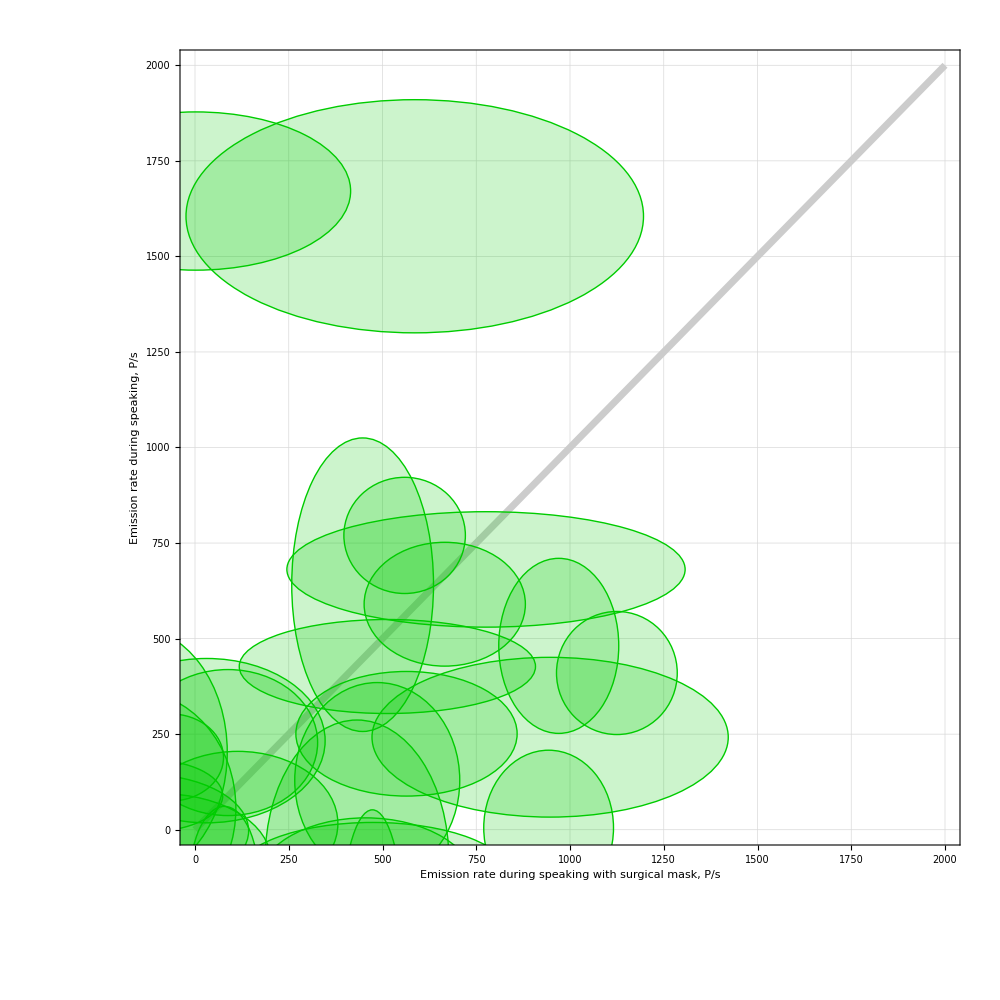

MultinormalDistribution[{2,1671},{{170569,0},{0,42849}}] | P34
MultinormalDistribution[{586,1605},{{372100,0},{0,93025}}] | P43
MultinormalDistribution[{559,770},{{26244,0},{0,23104}}] | P14
MultinormalDistribution[{776,681},{{281961,0},{0,22801}}] | P12
MultinormalDistribution[{447,641},{{35721,0},{0,147456}}] | P2
MultinormalDistribution[{666,590},{{46225,0},{0,26244}}] | P37
MultinormalDistribution[{970,481},{{25600,0},{0,52441}}] | P35
MultinormalDistribution[{513,427},{{156025,0},{0,15129}}] | P11
MultinormalDistribution[{1125,410},{{25921,0},{0,25921}}] | P10
MultinormalDistribution[{564,251},{{87025,0},{0,26569}}] | P5
MultinormalDistribution[{947,242},{{225625,0},{0,43681}}] | P33
MultinormalDistribution[{31,233},{{99856,0},{0,46225}}] | P8
MultinormalDistribution[{88,228},{{57121,0},{0,36481}}] | P6
MultinormalDistribution[{-163,203},{{62001,0},{0,106929}}] | P42
MultinormalDistribution[{-66,189},{{20164,0},{0,12996}}] | P26
MultinormalDistribution[{486,129},{{48400,0},{0,65536}}] | P19
MultinormalDistribution[{-122,89},{{38416,0},{0,8836}}] | P32
MultinormalDistribution[{-164,56},{{74529,0},{0,94249}}] | P25
MultinormalDistribution[{114,16},{{71289,0},{0,35721}}] | P40
MultinormalDistribution[{943,5},{{29929,0},{0,41209}}] | P3
MultinormalDistribution[{-136,-3},{{77841,0},{0,21904}}] | P21
MultinormalDistribution[{432,-79},{{60025,0},{0,133956}}] | P16
MultinormalDistribution[{-89,-80},{{84681,0},{0,30276}}] | P17
MultinormalDistribution[{474,-121},{{135424,0},{0,19600}}] | P20
MultinormalDistribution[{78,-137},{{8649,0},{0,39204}}] | P38
MultinormalDistribution[{455,-144},{{85849,0},{0,30625}}] | P15
MultinormalDistribution[{473,-260},{{6889,0},{0,97344}}] | P41

27

```mathematica
G
TableForm[SortBy[M,-#[[1,1,2]]&]]
Length[M]
```

```mathematica
Mean[LogNormalDistribution[4.908506526878052,1.3066696748075992]]        (*    Sprechen ohne MNS    *)
Mean[LogNormalDistribution[5.629049008402892,0.8450425746478247]]        (*    Sprechen mit  MNS    *)
%/%%
```

318.047

397.859

1.25094

```mathematica
M = Select[M,MemberQ[{"P34","P43"},Last[#]]&]
```

{{MultinormalDistribution[{2,1671},{{170569,0},{0,42849}}],P34},{MultinormalDistribution[{586,1605},{{372100,0},{0,93025}}],P43}}

```mathematica
Clear[a,h,m,s,Δm,Δs]
```

```mathematica
h = M[[2]][[1]]
```

MultinormalDistribution[{586,1605},{{372100,0},{0,93025}}]

```mathematica
h = MultinormalDistribution[{m    ,s       },{{Δm          ,0},{0,Δs       }}]
```

MultinormalDistribution[{m,s},{{Δm,0},{0,Δs}}]

```mathematica
h = PDF[h,{x,y}]
```

(ⅇ^(1/2 (-(-m+x)^2/Δm-(-s+y)^2/Δs)))/(2 π √(Δm Δs))

```mathematica
h = h/.(x->a*y)
```

(ⅇ^(1/2 (-(-m+a y)^2/Δm-(-s+y)^2/Δs)))/(2 π √(Δm Δs))

```mathematica
ExpressionVariables[h]
```

ExpressionVariables[(ⅇ^(1/2 (-(-m+a y)^2/Δm-(-s+y)^2/Δs)))/(2 π √(Δm Δs))]

```mathematica
h = Integrate[h,{y,0,Infinity},Assumptions->{(a|m|s|Δm|Δs)∈Reals,a>0,Δm>0,Δs>0}]
```

(ⅇ^(-(m-a s)^2/(2 (Δm+a^2 Δs))) (1+Erf[(s Δm+a m Δs)/(√2 √(Δm Δs (Δm+a^2 Δs)))]))/(2 √(2 π) √(Δm+a^2 Δs))

```mathematica
ExpressionVariables[h]
```

{a,m,s,Δm,Δs}

```mathematica
h = Simplify[h,Assumptions->{(a|m|s|Δm|Δs)∈Reals,a>0,Δm>0,Δs>0}]
```

(ⅇ^(-(m-a s)^2/(2 (Δm+a^2 Δs))) (1+Erf[(s Δm+a m Δs)/(√2 √(Δm Δs (Δm+a^2 Δs)))]))/(2 √(2 π) √(Δm+a^2 Δs))

```mathematica
Lges[a_] = h
ExpressionVariables[%]
```

(ⅇ^(-(m-a s)^2/(2 (Δm+a^2 Δs))) (1+Erf[(s Δm+a m Δs)/(√2 √(Δm Δs (Δm+a^2 Δs)))]))/(2 √(2 π) √(Δm+a^2 Δs))

{a,m,s,Δm,Δs}

```mathematica
h = h/.{m->Subscript[m, i],s->Subscript[s, i],Δm->Subscript[Δm, i],Δs->Subscript[Δs, i]}
```

(ⅇ^(-(m_i-a s_i)^2/(2 (Δm_i+a^2 Δs_i))) (1+Erf[(s_i Δm_i+a m_i Δs_i)/(√2 √(Δm_i Δs_i (Δm_i+a^2 Δs_i)))]))/(2 √(2 π) √(Δm_i+a^2 Δs_i))

```mathematica
TraditionalForm[h]
```

(ⅇ^(-(m_i-a s_i)^2/(2 (a^2 Δs_i+Δm_i))) (erf((a Δs_i m_i+Δm_i s_i)/(√2 √(Δm_i Δs_i (a^2 Δs_i+Δm_i))))+1))/(2 √(2 π) √(a^2 Δs_i+Δm_i))

```mathematica
Clear[a,L,Lges]
L = Map[(
h = PDF[#[[1]],{x,y}];
h = h/.(x->a*y);
h = Integrate[h,{y,0,Infinity},Assumptions->{a∈Reals,a>0}];
ReplacePart[#,h,1]
)&,M]
```

{{(ⅇ^(-(2-1671 a)^2/(341138+85698 a^2)) (1+Erf[(95006933+28566 a)/(28497 √(341138+85698 a^2))]))/(2 √(341138+85698 a^2) √π),P34},{(ⅇ^(-(586-1605 a)^2/(186050 (4+a^2))) (1+Erf[(3210+293 a)/(305 √2 √(4+a^2))]))/(610 √(4+a^2) √(2 π)),P43}}

```mathematica
i = Length[L];
```

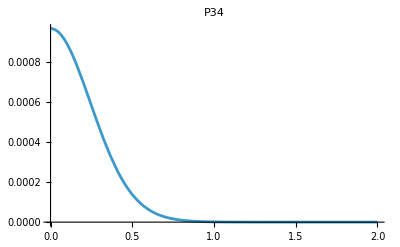

```mathematica
If[i>0,h=L[[i--]];Plot[h[[1]],{a,0,2},PlotRange->All,PlotLabel->h[[2]]]]
```

```mathematica
Lges[a_] = Simplify[Times@@First/@L]
```

(ⅇ^(-(586-1605 a)^2/(186050 (4+a^2))-(2-1671 a)^2/(341138+85698 a^2)) (1+Erf[(3210+293 a)/(305 √2 √(4+a^2))]) (1+Erf[(95006933+28566 a)/(28497 √(341138+85698 a^2))]))/(2440 √(4+a^2) √(170569+42849 a^2) π)

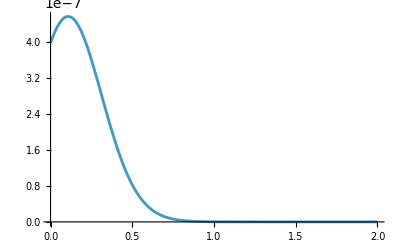

```mathematica
Plot[Lges[a],{a,0,2},PlotRange->All]
```

```mathematica
FindMaximum[Lges[a],{a,0,0.6}]
```

{4.56774×10^-7,{a→0.111049}}

```mathematica
n = 1/First[%]
```

2.18927×10^6

```mathematica
l = Interpolation[Map[{#,n*Lges[#]}&,Range[0,1.5,0.001]]]
```

InterpolatingFunction[…]

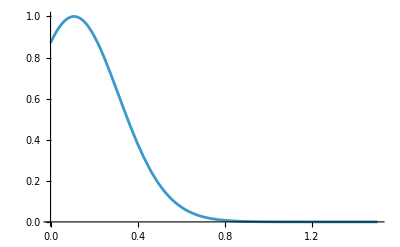

```mathematica
Plot[l[a],{a,0,1.5},PlotRange->All]
```

```mathematica
n = 1/Integrate[l[a],{a,0,1.5}]
```

2.71843

```mathematica
f[a_] = n*l[a]
```

2.71843 InterpolatingFunction[…][a]

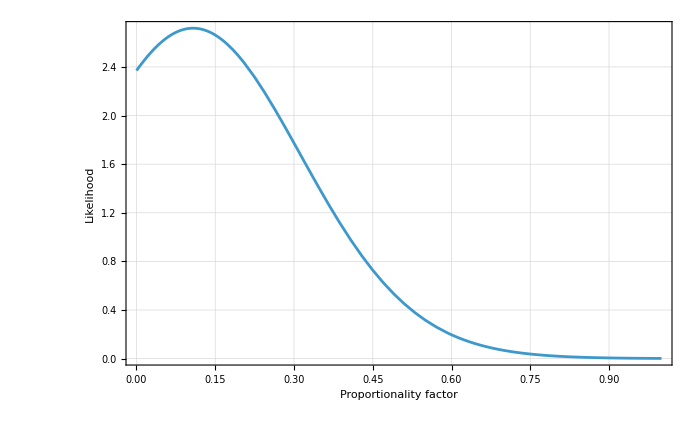

```mathematica
P = Plot[
f[a],{a,0,1},
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Proportionality factor","Likelihood"},
FrameTicks->{Automatic,None},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotRange->{All,{0,All}}]
```

```mathematica
NIntegrate[f[x],{x,0,1.5}]
```

1.

```mathematica
EV = NIntegrate[x*f[x],{x,0,1.5}]                                                   (*    Mean oder Expectation     *)
```

0.216166

```mathematica
Med = q/.FindRoot[NIntegrate[f[x],{x,0,q}] ==0.5,{q,0.2}]                     (*    Median     *)
```

NIntegrate::nlim: x = q is not a valid limit of integration.

0.190827

```mathematica
CIlo = q/.FindRoot[NIntegrate[f[x],{x,0,q}] ==0.025,{q,0}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

0.0104135

```mathematica
CIhi = q/.FindRoot[NIntegrate[f[x],{x,0,q}] ==0.975,{q,0.5}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

0.568433

```mathematica
NIntegrate[f[x],{x,CIlo,CIhi}]
```

0.95

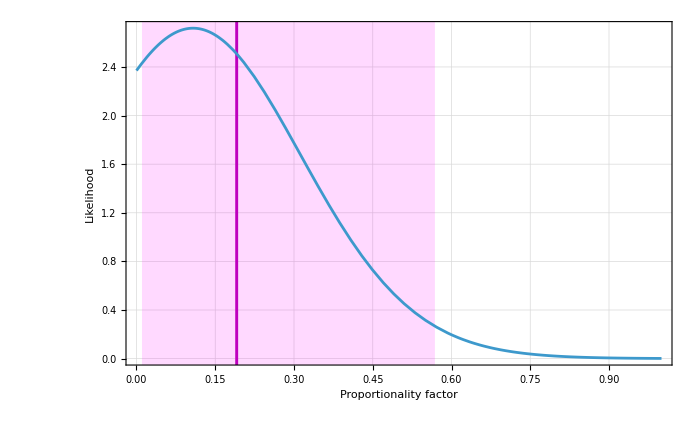

```mathematica
5/6;
Append[P,Prolog->{
{Hue[%,1,0.7],Thickness[0.003],Line[{{Med,-1},{Med,4}}]},
{Hue[%,1,1,0.15],Rectangle[{CIlo,-1},{CIhi,4}]}}]
```

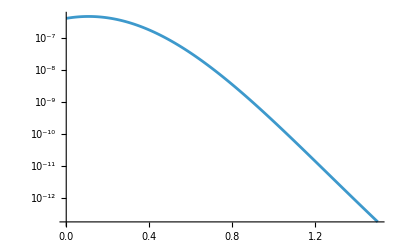

```mathematica
LogPlot[Lges[a],{a,0,1.5},PlotPoints->1200]
```

```mathematica
S = Range[0,1.0,0.01];
S = Map[{#,NIntegrate[f[x],{x,0,#}]}&,S]
```

{{0.,0.},{0.01,0.0239953},{0.02,0.0485517},{0.03,0.0736228},{0.04,0.0991592},{0.05,0.125108},{0.06,0.151413},{0.07,0.178018},{0.08,0.20486},{0.09,0.231879},{0.1,0.259012},{0.11,0.286195},{0.12,0.313363},{0.13,0.340453},{0.14,0.367403},{0.15,0.394149},{0.16,0.420631},{0.17,0.446792},{0.18,0.472574},{0.19,0.497925},{0.2,0.522794},{0.21,0.547135},{0.22,0.570904},{0.23,0.594061},{0.24,0.616573},{0.25,0.638407},{0.26,0.659536},{0.27,0.679938},{0.28,0.699593},{0.29,0.718488},{0.3,0.736613},{0.31,0.753961},{0.32,0.770529},{0.33,0.786319},{0.34,0.801336},{0.35,0.815587},{0.36,0.829083},{0.37,0.841838},{0.38,0.853867},{0.39,0.86519},{0.4,0.875825},{0.41,0.885796},{0.42,0.895125},{0.43,0.903836},{0.44,0.911955},{0.45,0.919507},{0.46,0.926519},{0.47,0.933017},{0.48,0.939029},{0.49,0.944579},{0.5,0.949695},{0.51,0.954403},{0.52,0.958726},{0.53,0.96269},{0.54,0.966319},{0.55,0.969634},{0.56,0.97266},{0.57,0.975415},{0.58,0.97792},{0.59,0.980195},{0.6,0.982258},{0.61,0.984125},{0.62,0.985812},{0.63,0.987334},{0.64,0.988707},{0.65,0.989942},{0.66,0.991051},{0.67,0.992047},{0.68,0.99294},{0.69,0.993739},{0.7,0.994453},{0.71,0.995091},{0.72,0.995659},{0.73,0.996166},{0.74,0.996616},{0.75,0.997016},{0.76,0.997372},{0.77,0.997686},{0.78,0.997965},{0.79,0.998212},{0.8,0.99843},{0.81,0.998623},{0.82,0.998793},{0.83,0.998942},{0.84,0.999074},{0.85,0.99919},{0.86,0.999292},{0.87,0.999381},{0.88,0.99946},{0.89,0.999529},{0.9,0.999589},{0.91,0.999642},{0.92,0.999688},{0.93,0.999728},{0.94,0.999764},{0.95,0.999794},{0.96,0.999821},{0.97,0.999845},{0.98,0.999865},{0.99,0.999883},{1.,0.999898}}

```mathematica
Clear[f,g,h,s,y,µ,σ]
f = PDF[LogNormalDistribution[µ,σ],#]&;
g = CDF[LogNormalDistribution[µ,σ],#]&;
s = Select[S,(0.001≤#[[2]]≤0.999)&];
Length[s]
```

83

```mathematica
h = Nearest[Rule@@@Reverse/@s];
h = First/@h/@{0.5,0.9,0.1};
h = Join[{Log[First[h]],Log[Divide@@Rest[h]]/E},h]
```

{-1.66073,0.873679,0.19,0.43,0.04}

```mathematica
y = Transpose[s];
y = y[[2]]-g/@y[[1]];
y = FindMinimum[y.y,
{{µ,h[[1]]},
{σ,h[[2]]}}]
```

CompiledFunction::cfsa: Argument µ at position 2 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

{0.0930801,{µ→-1.72482,σ→0.732382}}

```mathematica
{f[z],g[z]}/.y[[2]];
Clear[f,g];
{f[z_],g[z_]} = %%;
y = LogNormalDistribution@@Last/@Last[y];
y = Prepend[
Prepend[h=
{  γ->    Median[y],
CI->Quantile[y,{0.025,0.975}]},
FindMaximum[PDF[y,ML],{ML,h[[2,2,1]],h[[1,2]]}][[2,1]]],
y]
```

{LogNormalDistribution[-1.72482,0.732382],ML→0.104224,γ→0.178204,CI→{0.0424144,0.748726}}

```mathematica
Map[ReplacePart[#,Round[#[[2]],0.001],2]&,Rest[y]]
```

{ML→0.104,γ→0.178,CI→{0.042,0.749}}

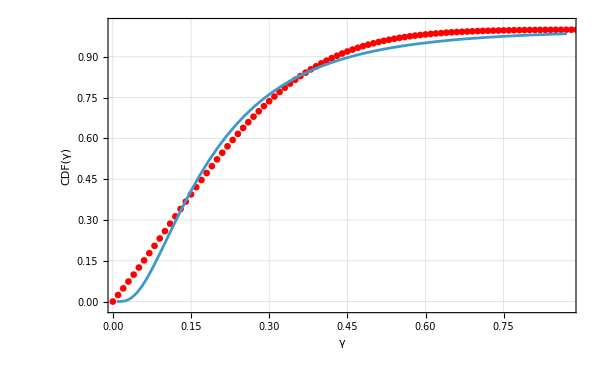

```mathematica
Plot[g[z],Prepend[{0.8,1.05}*s[[{1,-1},1]],z],
Axes->False,
Prolog->{Red,PointSize[0.008],Point[S]},
Frame->True,
FrameLabel->{"γ","CDF(γ)"},
GridLines->Automatic,
ImageSize->600,
LabelStyle->MyTS,
PlotRange->{All,{-0.02,1.02}},
PlotRangeClipping->True]
```